# Research Project ACM 40730: Mathematica for research Azam Jainullabudin Mohamed (18201501)

## Introduction:

The versatility of Mathematica with respect to data visualization and data manipulation plays a significant role in data interpretations. The project is about identifying the object in the image given by the user and visualizing data in accordance with it. For instance, I am trying to identify the fruit from the user image and perform visualization of data using the dataset. In this regard, the user can see the country in which that particular fruit is produced maximum. In this project, I have used Machine learning function “Classify” using logistic regression method on my unsupervised trained data. In doing so, I am able to identify the fruits from the given image with 90 % accuracy.

## Implementation and execution:

### Image Identification:

#### Steps involved in Image identification process:

1. Importing the image.
2. Classifying the related images.
3. Training the dataset of images.
4. Feeding the dataset to Machine learning function.
5. Testing with out of box sample images.

#### Training data and applying Machine learning algorithm:

True

True

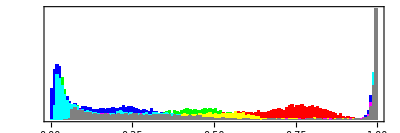

```mathematica
(* To check if the expression with image cannot be sub divided *)
AtomQ[-Graphics-]
(* To check if the image is valid using ImageQ *)
ImageQ[-Graphics-]
(* To plot a histogram of the pixel levels in image using Image histogram *)
ImageHistogram[-Graphics-]
```

```mathematica
(* Buidling Training data from the fruit dataset *)
(* Location of Fruit Dataset *)
locationapple = "D:\\Azam M S\\Mathematica\\Fruit_Dataset\\Apple\\";
locationcherry = "D:\\Azam M S\\Mathematica\\Fruit_Dataset\\Cherry\\";
locationavacado="D:\\Azam M S\\Mathematica\\Fruit_Dataset\\Avacado\\";
locationbanana="D:\\Azam M S\\Mathematica\\Fruit_Dataset\\Banana\\";
locationdates="D:\\Azam M S\\Mathematica\\Fruit_Dataset\\Dates\\";
locationpomo="D:\\Azam M S\\Mathematica\\Fruit_Dataset\\Pomo\\";
locationstrawberry="D:\\Azam M S\\Mathematica\\Fruit_Dataset\\Strawberry\\";
locationwalnut="D:\\Azam M S\\Mathematica\\Fruit_Dataset\\Walnut\\";
locationpine="D:\\Azam M S\\Mathematica\\Fruit_Dataset\\Pineapple\\";
```

```mathematica
extn2="_200.jpg";
avacado= Table[Import[FileNameJoin[{locationavacado,ToString[i]<>extn2}]],{i,1,10}]; (* Importing and training Avacado fruit Image *)
avacadotrainingset = Table[avacadodata -> "Avacado", {avacadodata, avacado}]
```

{-Graphics-→Avacado,-Graphics-→Avacado,-Graphics-→Avacado,-Graphics-→Avacado,-Graphics-→Avacado,-Graphics-→Avacado,-Graphics-→Avacado,-Graphics-→Avacado,-Graphics-→Avacado,-Graphics-→Avacado}

```mathematica
apple = Map[Import, FileNames["*_100.jpg", locationapple]];  (* Importing the Image *)
(* Training Apple image *)
appletrainingset = Table[appledata-> "Apple", {appledata, apple}]
```

{-Graphics-→Apple,-Graphics-→Apple,-Graphics-→Apple,-Graphics-→Apple,-Graphics-→Apple,-Graphics-→Apple,-Graphics-→Apple,-Graphics-→Apple,-Graphics-→Apple,-Graphics-→Apple,-Graphics-→Apple,-Graphics-→Apple,-Graphics-→Apple,-Graphics-→Apple,-Graphics-→Apple,-Graphics-→Apple,-Graphics-→Apple,-Graphics-→Apple,-Graphics-→Apple,-Graphics-→Apple}

```mathematica
cherry = Map[Import, FileNames["*_400.jpg", locationcherry]]; (* Importing and training Cherry fruit Image *)
(* Training Cherry image *)
cherrytrainingset = Table[cherrydata-> "Cherry", {cherrydata, cherry}]
```

{-Graphics-→Cherry,-Graphics-→Cherry,-Graphics-→Cherry,-Graphics-→Cherry,-Graphics-→Cherry,-Graphics-→Cherry,-Graphics-→Cherry,-Graphics-→Cherry,-Graphics-→Cherry,-Graphics-→Cherry,-Graphics-→Cherry,-Graphics-→Cherry,-Graphics-→Cherry,-Graphics-→Cherry,-Graphics-→Cherry,-Graphics-→Cherry}

```mathematica
banana = Map[Import, FileNames["*", locationbanana]]; (* Importing and training Banana fruit Image *)
bananatrainingset = Table[bananadata-> "Banana", {bananadata, banana}]
```

{-Graphics-→Banana,-Graphics-→Banana,-Graphics-→Banana,-Graphics-→Banana,-Graphics-→Banana,-Graphics-→Banana,-Graphics-→Banana,-Graphics-→Banana,-Graphics-→Banana,-Graphics-→Banana,-Graphics-→Banana,-Graphics-→Banana,-Graphics-→Banana,-Graphics-→Banana,-Graphics-→Banana,-Graphics-→Banana,-Graphics-→Banana,-Graphics-→Banana,-Graphics-→Banana,-Graphics-→Banana,-Graphics-→Banana,-Graphics-→Banana,-Graphics-→Banana,-Graphics-→Banana,-Graphics-→Banana,-Graphics-→Banana,-Graphics-→Banana,-Graphics-→Banana,-Graphics-→Banana,-Graphics-→Banana,-Graphics-→Banana,-Graphics-→Banana,-Graphics-→Banana,-Graphics-→Banana,-Graphics-→Banana}

```mathematica
dates= Map[Import, FileNames["*", locationdates]]; (* Importing and training Dates fruit Image *)
datestrainingset = Table[datesdata-> "Dates", {datesdata, dates}]
```

{-Graphics-→Dates,-Graphics-→Dates,-Graphics-→Dates,-Graphics-→Dates,-Graphics-→Dates,-Graphics-→Dates,-Graphics-→Dates,-Graphics-→Dates,-Graphics-→Dates,-Graphics-→Dates,-Graphics-→Dates,-Graphics-→Dates}

```mathematica
pomo = Map[Import, FileNames["*", locationpomo]]; (* Importing and training Pomo fruit Image *)
pomotrainingset = Table[pomodata-> "Pomegranate", {pomodata, pomo}]
```

{-Graphics-→Pomegranate,-Graphics-→Pomegranate,-Graphics-→Pomegranate,-Graphics-→Pomegranate,-Graphics-→Pomegranate,-Graphics-→Pomegranate,-Graphics-→Pomegranate,-Graphics-→Pomegranate,-Graphics-→Pomegranate,-Graphics-→Pomegranate,-Graphics-→Pomegranate,-Graphics-→Pomegranate,-Graphics-→Pomegranate,-Graphics-→Pomegranate,-Graphics-→Pomegranate,-Graphics-→Pomegranate,-Graphics-→Pomegranate}

```mathematica
strawberry = Map[Import, FileNames["*", locationstrawberry]]; (* Importing and training Strawberry fruit Image *)
strawberrytrainingset = Table[strawberrydata-> "Strawberry", {strawberrydata, strawberry}]
```

{-Graphics-→Strawberry,-Graphics-→Strawberry,-Graphics-→Strawberry,-Graphics-→Strawberry,-Graphics-→Strawberry,-Graphics-→Strawberry,-Graphics-→Strawberry,-Graphics-→Strawberry,-Graphics-→Strawberry,-Graphics-→Strawberry,-Graphics-→Strawberry,-Graphics-→Strawberry,-Graphics-→Strawberry,-Graphics-→Strawberry,-Graphics-→Strawberry}

```mathematica
walnut = Map[Import, FileNames["*", locationwalnut]]; (* Importing and training Walnut fruit Image *)
walnuttrainingset = Table[walnutdata-> "Walnut", {walnutdata, walnut}]
```

{-Graphics-→Walnut,-Graphics-→Walnut,-Graphics-→Walnut,-Graphics-→Walnut,-Graphics-→Walnut,-Graphics-→Walnut,-Graphics-→Walnut,-Graphics-→Walnut,-Graphics-→Walnut,-Graphics-→Walnut}

```mathematica
pine = Map[Import, FileNames["*", locationpine]]; (* Importing and training Pine fruit Image *)
pinetrainingset = Table[pinedata-> "Pine", {pinedata, pine}]
```

{-Graphics-→Pine,-Graphics-→Pine,-Graphics-→Pine,-Graphics-→Pine,-Graphics-→Pine,-Graphics-→Pine,-Graphics-→Pine,-Graphics-→Pine,-Graphics-→Pine,-Graphics-→Pine}

```mathematica
(* Building training set *)
trainingset = Join[appletrainingset, avacadotrainingset, bananatrainingset, datestrainingset, pomotrainingset, strawberrytrainingset, walnuttrainingset, cherrytrainingset, pinetrainingset]
(* Finding the length of training set *)
Length[trainingset]
```

{-Graphics-→Apple,-Graphics-→Apple,-Graphics-→Apple,-Graphics-→Apple,-Graphics-→Apple,-Graphics-→Apple,-Graphics-→Apple,-Graphics-→Apple,-Graphics-→Apple,-Graphics-→Apple,-Graphics-→Apple,-Graphics-→Apple,-Graphics-→Apple,-Graphics-→Apple,-Graphics-→Apple,-Graphics-→Apple,-Graphics-→Apple,-Graphics-→Apple,-Graphics-→Apple,-Graphics-→Apple,-Graphics-→Avacado,-Graphics-→Avacado,-Graphics-→Avacado,-Graphics-→Avacado,-Graphics-→Avacado,-Graphics-→Avacado,-Graphics-→Avacado,-Graphics-→Avacado,-Graphics-→Avacado,-Graphics-→Avacado,-Graphics-→Banana,-Graphics-→Banana,-Graphics-→Banana,-Graphics-→Banana,-Graphics-→Banana,-Graphics-→Banana,-Graphics-→Banana,-Graphics-→Banana,-Graphics-→Banana,-Graphics-→Banana,-Graphics-→Banana,-Graphics-→Banana,-Graphics-→Banana,-Graphics-→Banana,-Graphics-→Banana,-Graphics-→Banana,-Graphics-→Banana,-Graphics-→Banana,-Graphics-→Banana,-Graphics-→Banana,-Graphics-→Banana,-Graphics-→Banana,-Graphics-→Banana,-Graphics-→Banana,-Graphics-→Banana,-Graphics-→Banana,-Graphics-→Banana,-Graphics-→Banana,-Graphics-→Banana,-Graphics-→Banana,-Graphics-→Banana,-Graphics-→Banana,-Graphics-→Banana,-Graphics-→Banana,-Graphics-→Banana,-Graphics-→Dates,-Graphics-→Dates,-Graphics-→Dates,-Graphics-→Dates,-Graphics-→Dates,-Graphics-→Dates,-Graphics-→Dates,-Graphics-→Dates,-Graphics-→Dates,-Graphics-→Dates,-Graphics-→Dates,-Graphics-→Dates,-Graphics-→Pomegranate,-Graphics-→Pomegranate,-Graphics-→Pomegranate,-Graphics-→Pomegranate,-Graphics-→Pomegranate,-Graphics-→Pomegranate,-Graphics-→Pomegranate,-Graphics-→Pomegranate,-Graphics-→Pomegranate,-Graphics-→Pomegranate,-Graphics-→Pomegranate,-Graphics-→Pomegranate,-Graphics-→Pomegranate,-Graphics-→Pomegranate,-Graphics-→Pomegranate,-Graphics-→Pomegranate,-Graphics-→Pomegranate,-Graphics-→Strawberry,-Graphics-→Strawberry,-Graphics-→Strawberry,-Graphics-→Strawberry,-Graphics-→Strawberry,-Graphics-→Strawberry,-Graphics-→Strawberry,-Graphics-→Strawberry,-Graphics-→Strawberry,-Graphics-→Strawberry,-Graphics-→Strawberry,-Graphics-→Strawberry,-Graphics-→Strawberry,-Graphics-→Strawberry,-Graphics-→Strawberry,-Graphics-→Walnut,-Graphics-→Walnut,-Graphics-→Walnut,-Graphics-→Walnut,-Graphics-→Walnut,-Graphics-→Walnut,-Graphics-→Walnut,-Graphics-→Walnut,-Graphics-→Walnut,-Graphics-→Walnut,-Graphics-→Cherry,-Graphics-→Cherry,-Graphics-→Cherry,-Graphics-→Cherry,-Graphics-→Cherry,-Graphics-→Cherry,-Graphics-→Cherry,-Graphics-→Cherry,-Graphics-→Cherry,-Graphics-→Cherry,-Graphics-→Cherry,-Graphics-→Cherry,-Graphics-→Cherry,-Graphics-→Cherry,-Graphics-→Cherry,-Graphics-→Cherry,-Graphics-→Pine,-Graphics-→Pine,-Graphics-→Pine,-Graphics-→Pine,-Graphics-→Pine,-Graphics-→Pine,-Graphics-→Pine,-Graphics-→Pine,-Graphics-→Pine,-Graphics-→Pine}

145

```mathematica
(* Applying Machine learning classification function "Classify" to the training set *)
cs=Classify[trainingset]
```

ClassifierFunction[…]

#### Visualization of training dataset:

-Graphics-

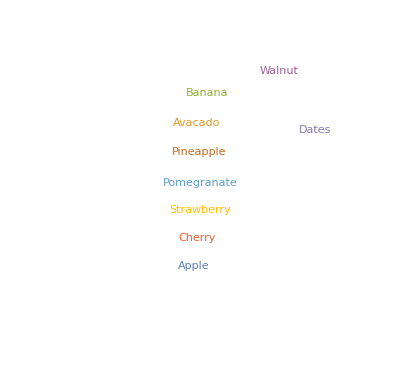

Dataset[<>]

```mathematica
(* Collage of all the fruits in training set *)
ImageCollage[{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-, -Graphics-}]
(* Word cloud of the fruits in the training set *) 
word = WordCloud[{"Apple", "Avacado", "Banana", "Cherry", "Dates", "Pomegranate","Strawberry", "Walnut","Pineapple"}, -Graphics-]
(* Statistics of specific fruit *)
stats={Total,Min, Max,Mean,Median,StandardDeviation};
Dataset[AssociationThread[Text/@stats->Through[stats[-Graphics-]]]]
```

```mathematica
(* List of all the fruits in the training set *)
fruitsList = {-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-, -Graphics-}
(* Checking the type of variable using Head function *)
Head[fruitsList]
(* Using Manipulate function to visualize the fruits in the training set by using slider *)
Manipulate[Show[fruit], {fruit,fruitsList}]
(* Using Animate function to visualize the one seen above in autorun mode without manually adjusting the slider *)
Animate[Show[fruit], {fruit,fruitsList}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

List

#### Testing with sample images:

```mathematica
(* Testing: Image identification using sample images *)
```

```mathematica
cs[Import["D:\\Azam M S\\Mathematica\\Fruit_Dataset\\apple_test.jpg"]] (* Testing a random sample image of apple *)
cs[-Graphics-]
cs[Import["D:\\Azam M S\\Mathematica\\Fruit_Dataset\\avocado_sample.jpg"]]  (* Testing a random sample image of avacado *)
cs[-Graphics-]
cs[Import["D:\\Azam M S\\Mathematica\\Fruit_Dataset\\pomo_sample.jpg"]] (* Testing a random sample image of pomegranate *)
cs[-Graphics-]
cs[Import["D:\\Azam M S\\Mathematica\\Fruit_Dataset\\cherry_sample.jpg"]] (* Testing a random sample image of cherry *)
cs[-Graphics-]
cs[Import["D:\\Azam M S\\Mathematica\\Fruit_Dataset\\walnut_sample.jpg"]] (* Testing a random image of walnut *)
cs[-Graphics-]
```

Apple

Apple

Avacado

Avacado

Pomegranate

Pomegranate

Cherry

Cherry

Walnut

Walnut

### Data Visualization:

#### Steps involved in Data visualization:

1. Import the country with fruit production dataset.
2. Create a list with all entries as per the dataset.
3. Identify the country with maximum production of a specific fruit based on the user’s input.
4. Perform Data Visualization of the country using Word plot, manipulate, CountryData and others.

#### Importing a dataset (csv file):

```mathematica
(* Importing dataset - Countries with production of fruits *)
dataset = Import["D:\\Azam M S\\Mathematica\\Dataset_fruits.csv", "Data"]
(* Displaying the dataset in viewable format *)
dataset1 = Import["D:\\Azam M S\\Mathematica\\Dataset_fruits.csv", "Dataset"]
```

{{,Apple,Avacado,Banana,Dates,Pomogranate,Strawberry,Walnut,Cherry,Pineapple},{Austria,40.36,0.49,13.18,39.83,27.39,40.57,1586.92,329.18,49.54},{Belgium,603.26,1.96,25.5,196.68,65.92,91.42,1660.42,7.33,42.2},{Bulgaria,34.99,1.79,1.65,27.02,6.72,8.37,531.99,108,4.64},{Croatia,19.03,0.88,6.11,31.03,8.21,14.32,320.62,42.62,6.28},{Cyprus,16.65,1.42,2.36,10.98,9.45,11.81,108.38,22.5,46.36},{Czech Republic,148.69,0.8,5.67,19.19,7.79,13.47,1319.87,65.29,13.64},{Denmark,25.8,0.81,18.57,35.94,19.88,38.45,3436.13,14.52,45.5},{Finland,28.22,1.61,19.23,28.33,31.74,50.97,1781.22,4.52,12.77},{France,367.19,1.53,19.49,157.79,30.06,49.54,1846.91,1.5,63.24},{Germany,156.9,0.81,8.65,55.01,33.55,42.2,1646.84,16.05,24.22},{Greece,14.96,0.79,1.12,39.75,3.52,4.64,923.72,27.39,4.18},{Hungary,127.8,1,3.84,14.64,2.45,6.28,1031.67,65.92,196.68},{Ireland,321.48,1.32,11.62,55.63,34.74,46.36,1500.6,6.72,27.02},{Latvia,26.89,4.08,3.02,39.22,10.62,13.64,976.14,8.21,31.03},{Liechtenstein,329.18,0,2.68,8.03,42.82,45.5,516.51,9.45,10.98},{Lithuania,7.33,5.75,5.31,54.43,7.46,12.77,688.78,7.79,19.19},{Luxembourg,108,0.89,12.08,98.41,51.16,63.24,1650.74,19.88,35.94},{Malta,42.62,0.93,5.36,56.37,18.87,24.22,2015.4,31.74,28.33},{Montenegro,22.5,2.73,0.8,25.08,3.38,4.18,132.94,30.06,363.54},{Northern Ireland (UK),65.29,1.25,38.66,43.85,116.89,155.54,1300.2,13.18,832.95},{Poland,14.52,0.75,3.24,21.42,1.4,4.64,363.54,25.5,545.72},{Portugal,4.52,0.96,3.61,149.13,21.24,24.86,832.95,1.65,317.71},{Romania,1.5,1.46,5.11,16.9,3.24,8.35,545.72,6.11,444.37},{Serbia,16.05,1.28,0.86,42.59,3.91,4.76,317.71,157.79,19.49},{Slovakia,35.05,0.89,1.6,9.94,10.29,11.9,444.37,55.01,8.65},{Slovenia,74.65,0.97,2.04,11.25,10.47,12.51,1105.16,39.75,1.12},{Spain,62.55,0.65,60.05,139.03,18.6,21.25,442.96,14.64,3.84},{Sweden,47.52,1.15,56.88,86.8,120.79,177.67,3828.01,55.63,11.62},{Switzerland,7.48,0.69,6.46,39.8,26.44,32.9,1772.66,39.22,3.02}}

Dataset[<>]

#### Extracting columns and recreating a list of it:

```mathematica
(* Extracting each column of fruits from the dataset *)
columncountry = dataset[[2;;, 1]] (* Extracting the column 1 - Countries *)
columnapple = dataset[[2;;, 2]] (* Extracting the column 2 - Apples *)
columnavacado = dataset[[2;;, 3]] (* Extracting the column 3 - Avacado *)
columnbanana  = dataset[[2;;, 4]] (* Extracting the column 4 - Banana *)
columndates = dataset[[2;;,5]] (* Extracting the column 5 - Dates *)
columnpomo = dataset[[2;;,6]] (* Extracting the column 6 - Pomo *)
columnstrawberry = dataset[[2;;, 7]] (* Extracting the column 7 - Strawberry *)
columnwalnut = dataset[[2;;, 8]] (* Extracting the column 8 - Walnut *)
columncherry = dataset[[2;;,9]] (* Extracting the column 9 - cherry *)
columnpineapple = dataset[[2;;, 10]] (* Extracting the column 10 - Pineapple *)
```

{Austria,Belgium,Bulgaria,Croatia,Cyprus,Czech Republic,Denmark,Finland,France,Germany,Greece,Hungary,Ireland,Latvia,Liechtenstein,Lithuania,Luxembourg,Malta,Montenegro,Northern Ireland (UK),Poland,Portugal,Romania,Serbia,Slovakia,Slovenia,Spain,Sweden,Switzerland}

{40.36,603.26,34.99,19.03,16.65,148.69,25.8,28.22,367.19,156.9,14.96,127.8,321.48,26.89,329.18,7.33,108,42.62,22.5,65.29,14.52,4.52,1.5,16.05,35.05,74.65,62.55,47.52,7.48}

{0.49,1.96,1.79,0.88,1.42,0.8,0.81,1.61,1.53,0.81,0.79,1,1.32,4.08,0,5.75,0.89,0.93,2.73,1.25,0.75,0.96,1.46,1.28,0.89,0.97,0.65,1.15,0.69}

{13.18,25.5,1.65,6.11,2.36,5.67,18.57,19.23,19.49,8.65,1.12,3.84,11.62,3.02,2.68,5.31,12.08,5.36,0.8,38.66,3.24,3.61,5.11,0.86,1.6,2.04,60.05,56.88,6.46}

{39.83,196.68,27.02,31.03,10.98,19.19,35.94,28.33,157.79,55.01,39.75,14.64,55.63,39.22,8.03,54.43,98.41,56.37,25.08,43.85,21.42,149.13,16.9,42.59,9.94,11.25,139.03,86.8,39.8}

{27.39,65.92,6.72,8.21,9.45,7.79,19.88,31.74,30.06,33.55,3.52,2.45,34.74,10.62,42.82,7.46,51.16,18.87,3.38,116.89,1.4,21.24,3.24,3.91,10.29,10.47,18.6,120.79,26.44}

{40.57,91.42,8.37,14.32,11.81,13.47,38.45,50.97,49.54,42.2,4.64,6.28,46.36,13.64,45.5,12.77,63.24,24.22,4.18,155.54,4.64,24.86,8.35,4.76,11.9,12.51,21.25,177.67,32.9}

{1586.92,1660.42,531.99,320.62,108.38,1319.87,3436.13,1781.22,1846.91,1646.84,923.72,1031.67,1500.6,976.14,516.51,688.78,1650.74,2015.4,132.94,1300.2,363.54,832.95,545.72,317.71,444.37,1105.16,442.96,3828.01,1772.66}

{329.18,7.33,108,42.62,22.5,65.29,14.52,4.52,1.5,16.05,27.39,65.92,6.72,8.21,9.45,7.79,19.88,31.74,30.06,13.18,25.5,1.65,6.11,157.79,55.01,39.75,14.64,55.63,39.22}

{49.54,42.2,4.64,6.28,46.36,13.64,45.5,12.77,63.24,24.22,4.18,196.68,27.02,31.03,10.98,19.19,35.94,28.33,363.54,832.95,545.72,317.71,444.37,19.49,8.65,1.12,3.84,11.62,3.02}

```mathematica
(* Transforming the column data's into a list as seen below *) 
data= {columncountry, columnapple, columnavacado, columnbanana, columndates,columnpomo,columnstrawberry, columnwalnut,columncherry, columnpineapple}
orderedData = Transpose[data]
```

{{Austria,Belgium,Bulgaria,Croatia,Cyprus,Czech Republic,Denmark,Finland,France,Germany,Greece,Hungary,Ireland,Latvia,Liechtenstein,Lithuania,Luxembourg,Malta,Montenegro,Northern Ireland (UK),Poland,Portugal,Romania,Serbia,Slovakia,Slovenia,Spain,Sweden,Switzerland},{40.36,603.26,34.99,19.03,16.65,148.69,25.8,28.22,367.19,156.9,14.96,127.8,321.48,26.89,329.18,7.33,108,42.62,22.5,65.29,14.52,4.52,1.5,16.05,35.05,74.65,62.55,47.52,7.48},{0.49,1.96,1.79,0.88,1.42,0.8,0.81,1.61,1.53,0.81,0.79,1,1.32,4.08,0,5.75,0.89,0.93,2.73,1.25,0.75,0.96,1.46,1.28,0.89,0.97,0.65,1.15,0.69},{13.18,25.5,1.65,6.11,2.36,5.67,18.57,19.23,19.49,8.65,1.12,3.84,11.62,3.02,2.68,5.31,12.08,5.36,0.8,38.66,3.24,3.61,5.11,0.86,1.6,2.04,60.05,56.88,6.46},{39.83,196.68,27.02,31.03,10.98,19.19,35.94,28.33,157.79,55.01,39.75,14.64,55.63,39.22,8.03,54.43,98.41,56.37,25.08,43.85,21.42,149.13,16.9,42.59,9.94,11.25,139.03,86.8,39.8},{27.39,65.92,6.72,8.21,9.45,7.79,19.88,31.74,30.06,33.55,3.52,2.45,34.74,10.62,42.82,7.46,51.16,18.87,3.38,116.89,1.4,21.24,3.24,3.91,10.29,10.47,18.6,120.79,26.44},{40.57,91.42,8.37,14.32,11.81,13.47,38.45,50.97,49.54,42.2,4.64,6.28,46.36,13.64,45.5,12.77,63.24,24.22,4.18,155.54,4.64,24.86,8.35,4.76,11.9,12.51,21.25,177.67,32.9},{1586.92,1660.42,531.99,320.62,108.38,1319.87,3436.13,1781.22,1846.91,1646.84,923.72,1031.67,1500.6,976.14,516.51,688.78,1650.74,2015.4,132.94,1300.2,363.54,832.95,545.72,317.71,444.37,1105.16,442.96,3828.01,1772.66},{329.18,7.33,108,42.62,22.5,65.29,14.52,4.52,1.5,16.05,27.39,65.92,6.72,8.21,9.45,7.79,19.88,31.74,30.06,13.18,25.5,1.65,6.11,157.79,55.01,39.75,14.64,55.63,39.22},{49.54,42.2,4.64,6.28,46.36,13.64,45.5,12.77,63.24,24.22,4.18,196.68,27.02,31.03,10.98,19.19,35.94,28.33,363.54,832.95,545.72,317.71,444.37,19.49,8.65,1.12,3.84,11.62,3.02}}

{{Austria,40.36,0.49,13.18,39.83,27.39,40.57,1586.92,329.18,49.54},{Belgium,603.26,1.96,25.5,196.68,65.92,91.42,1660.42,7.33,42.2},{Bulgaria,34.99,1.79,1.65,27.02,6.72,8.37,531.99,108,4.64},{Croatia,19.03,0.88,6.11,31.03,8.21,14.32,320.62,42.62,6.28},{Cyprus,16.65,1.42,2.36,10.98,9.45,11.81,108.38,22.5,46.36},{Czech Republic,148.69,0.8,5.67,19.19,7.79,13.47,1319.87,65.29,13.64},{Denmark,25.8,0.81,18.57,35.94,19.88,38.45,3436.13,14.52,45.5},{Finland,28.22,1.61,19.23,28.33,31.74,50.97,1781.22,4.52,12.77},{France,367.19,1.53,19.49,157.79,30.06,49.54,1846.91,1.5,63.24},{Germany,156.9,0.81,8.65,55.01,33.55,42.2,1646.84,16.05,24.22},{Greece,14.96,0.79,1.12,39.75,3.52,4.64,923.72,27.39,4.18},{Hungary,127.8,1,3.84,14.64,2.45,6.28,1031.67,65.92,196.68},{Ireland,321.48,1.32,11.62,55.63,34.74,46.36,1500.6,6.72,27.02},{Latvia,26.89,4.08,3.02,39.22,10.62,13.64,976.14,8.21,31.03},{Liechtenstein,329.18,0,2.68,8.03,42.82,45.5,516.51,9.45,10.98},{Lithuania,7.33,5.75,5.31,54.43,7.46,12.77,688.78,7.79,19.19},{Luxembourg,108,0.89,12.08,98.41,51.16,63.24,1650.74,19.88,35.94},{Malta,42.62,0.93,5.36,56.37,18.87,24.22,2015.4,31.74,28.33},{Montenegro,22.5,2.73,0.8,25.08,3.38,4.18,132.94,30.06,363.54},{Northern Ireland (UK),65.29,1.25,38.66,43.85,116.89,155.54,1300.2,13.18,832.95},{Poland,14.52,0.75,3.24,21.42,1.4,4.64,363.54,25.5,545.72},{Portugal,4.52,0.96,3.61,149.13,21.24,24.86,832.95,1.65,317.71},{Romania,1.5,1.46,5.11,16.9,3.24,8.35,545.72,6.11,444.37},{Serbia,16.05,1.28,0.86,42.59,3.91,4.76,317.71,157.79,19.49},{Slovakia,35.05,0.89,1.6,9.94,10.29,11.9,444.37,55.01,8.65},{Slovenia,74.65,0.97,2.04,11.25,10.47,12.51,1105.16,39.75,1.12},{Spain,62.55,0.65,60.05,139.03,18.6,21.25,442.96,14.64,3.84},{Sweden,47.52,1.15,56.88,86.8,120.79,177.67,3828.01,55.63,11.62},{Switzerland,7.48,0.69,6.46,39.8,26.44,32.9,1772.66,39.22,3.02}}

```mathematica
(* Finding the length of dataset entries *)
```

```mathematica
lengthOfDataset = Length[columnapple]
```

29

#### Visualization data using dataset inputs:

```mathematica
(* 1. Identifying and extracting the fruit column as specified by user input using "Switch" command *)
(* 2. Accepting the user input using "countryWithMaxProd" function and converting it to lowercase *)
(* 3. Iterating the Dataset to identify the country with maximum production of user specified fruit using "For" loop *)
(* 4. Identifying the maximum production of apples using Max function *) 
(* 5. Highlight the country with Maximum production of user input fruit using WordCloud *)
(* 6. Displaying the pictorial representation of the country with the maximum production of the fruit specified by user *)
(* 7. Displaying the pictorial representation of the country with the maximum production of the fruit specified by user *)
(* 8. Graphical representation of country with maximum production *)
(* 9. Ploting the column of fruit specified by user using Sine function *)
```

2

Belgium

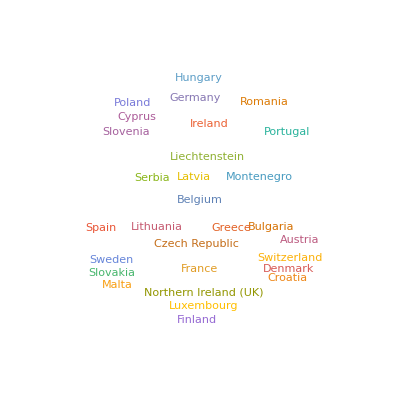

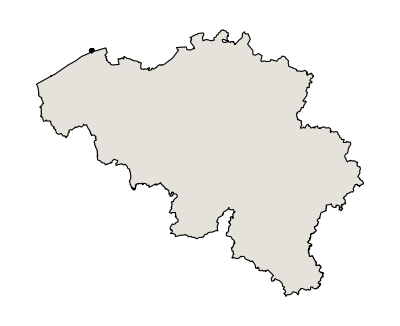

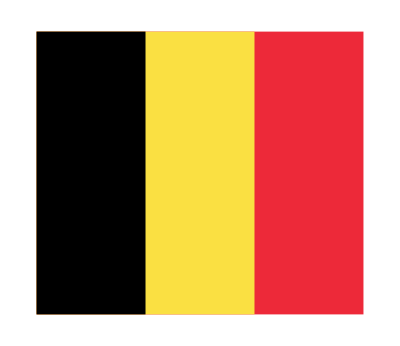

-Graphics-

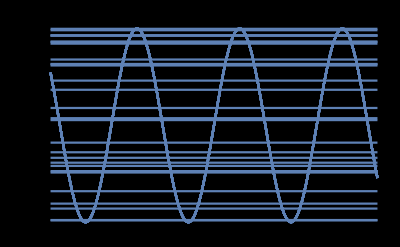

```mathematica
countryWithMaxProd[columnname_]:= Switch[ToLowerCase[columnname], "apple",j=2, "avacado", j=3,"banana", j=4, "dates", j=5, "pomegranate", j=6, "strawberry" , j=7, "walnut", j=8, "cherry", j=9, "pineapple", j=10, _, "Specified fruit is not present in the dataset"]
countryWithMaxProd["ApPlE"]
For[i=1, i≤ lengthOfDataset, i++,  If[orderedData[[i]][[j]] == Max[data[[j]]],Break[]]]; countryHavingMaximumProduction = orderedData[[i]][[1]]
wordcloud = {columncountry, data[[j]]};
wordclouddata = Transpose[wordcloud];
WordCloud[wordclouddata, Disk[]]
CountryData[countryHavingMaximumProduction, "Shape"]
CountryData[countryHavingMaximumProduction, "Flag"]
Graphics[{Gray,CountryData[countryHavingMaximumProduction,"Polygon"]},Frame->True]
Plot[Table[{Sin[x], Sin[y]}, {x, data[[j]]}], {y,-10,10}, Frame->True,Background->Black,PlotLabel->"Sin function of fruit productions"]
```

## Conclusion

Mathematica offers splendid range of options for Machine learning techniques and Data visualization. As seen above, it offers a accuracy level of 90 % in image identification using logistic regression. Having this Image identification as basic and as a next level of advancement,  we can try implementing Android features such as Face detection using Mathematica with much better level of accuracy.

#### Applications:

1. Face recognition feature.
2. Sentimental Analysis.
3. Detecting the objects in Military and Commercial applications.